# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Desktop\\QMB.wl"];
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# <r> open

```mathematica
J=1;
glist=Table[10^i,{i,-5,1.3,0.1}];
newglist=Partition[glist,4];
hlist=Table[10^i,{i,-4,1.1,0.1}];
newhlist=Partition[hlist,4];
```

```mathematica
Do[

basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];

DistributeDefinitions[IsingNNOpenHamiltonian,Beven,Bodd];

data1={};
SetSharedVariable[data1];
Do[
ParallelDo[
	Module[{H, eigenvals,Heven,Hodd,eveneigenval,oddeigenval},
H = IsingNNOpenHamiltonian[1,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
eveneigenval=Sort[Eigenvalues[N[Heven]]];
oddeigenval=Sort[Eigenvalues[N[Hodd]]];
AppendTo[data1,{{g,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{g,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {g,k},Method->"CoarsestGrained"];
,{k,newglist}];
Export["r_L_"<>ToString[L]<>"_h_1_log_g.m",Quiet[Sort[data1]]];

(*data2={};
SetSharedVariable[data2];
Do[
ParallelDo[
	Module[{H, eigenvals,Heven,Hodd,eveneigenval,oddeigenval},
H = IsingNNOpenHamiltonian[h,1,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
eveneigenval=Sort[Eigenvalues[N[Heven]]];
oddeigenval=Sort[Eigenvalues[N[Hodd]]];
AppendTo[data2,{{h,Quiet[MeanLevelSpacingRatio[eveneigenval]]},{h,Quiet[MeanLevelSpacingRatio[oddeigenval]]}}];
	]
, {h,k},Method->"CoarsestGrained"];
,{k,newhlist}];
Export["r_L_"<>ToString[L]<>"_g_1_log_h.m",Quiet[Sort[data2]]];

dim=2^L; (*Dimension of the Hilbert space*)
basisStates=IntegerDigits[Range[0,dim-1],2,L];
TranslateState[state_List]:=RotateLeft[state];
orbits={};
visited=Association[];
Do[If[!KeyExistsQ[visited,state],orbit=NestList[TranslateState,state,L-1];
orbit=DeleteDuplicates[orbit];
(*Mark all states in the orbit as visited*)Scan[(visited[#]=True)&,orbit];
AppendTo[orbits,orbit];],{state,basisStates}];
(*Creating momentum states*)
momentumEigenstates={};
Do[orbitSize=Length[orbit];
Do[k=2 Pi m/orbitSize;
stateSum=ConstantArray[0,dim];
Do[translatedState=Nest[TranslateState,orbit[[1]],n];
index=Position[basisStates,translatedState][[1,1]];
stateSum[[index]]+=Exp[-I k n];,{n,0,orbitSize-1}];
normalizedState=stateSum/Norm[stateSum];
AppendTo[momentumEigenstates,{k,normalizedState}];,{m,0,orbitSize-1}];,{orbit,orbits}];
(*Sorting everything*)
ks=First/@momentumEigenstates;
perm=OrderingBy[momentumEigenstates,First];
sortedKEigen=ks[[perm]];
sortedStates=(Last/@momentumEigenstates)[[perm]];
sortedPairs=Transpose[{sortedKEigen,sortedStates}];
dimensions=Tally[sortedKEigen];
glist=Table[10^i,{i,-5,1.3,0.1}];
newglist=Partition[glist,4];
J=1;
h=1;
klist=DeleteDuplicates[ks];

alldata={};
Do[
H=IsingNNClosedHamiltonian[1,g,J,L];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
val=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,blocks},DistributedContexts->Full];
ratios=Table[{g,MeanLevelSpacingRatio[i]},{i,val}];
AppendTo[alldata,ratios];
,{g,glist}];
Export["r_CLOSED_L_"<>ToString[L]<>"_g_1_log_h.m",alldata];

alldata={};
Do[
H=IsingNNClosedHamiltonian[h,1,J,L];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].H.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
val=ParallelTable[Sort[Chop[Eigenvalues[i]]],{i,blocks},DistributedContexts->Full];
ratios=Table[{h,MeanLevelSpacingRatio[i]},{i,val}];
AppendTo[alldata,ratios];
,{h,hlist}];
Export["r_CLOSED_L_"<>ToString[L]<>"_h_1_log_g.m",alldata];*)

,{L,4,6,2}]
```

# Results

```mathematica
J=1;
glist=Table[10^i,{i,-5,1.3,0.1}];
newglist=Partition[glist,4];
hlist=Table[10^i,{i,-4,1.1,0.1}];
newhlist=Partition[hlist,4];
```

## g

```mathematica
L=15;
data=Import["C:\\Users\\Miguel\\Desktop\\r_L_15_h_1_log_g.m"];
```

```mathematica
L=14;
data=Import["C:\\Users\\Miguel\\Desktop\\r_L_14_h_1_log_g.m"];
```

```mathematica
L=13;
data=Import["C:\\Users\\Miguel\\Desktop\\r_L_13_h_1_log_g.m"];
```

```mathematica
L=12;
data=Import["C:\\Users\\Miguel\\Desktop\\r_L_12_h_1_log_g.m"];
```

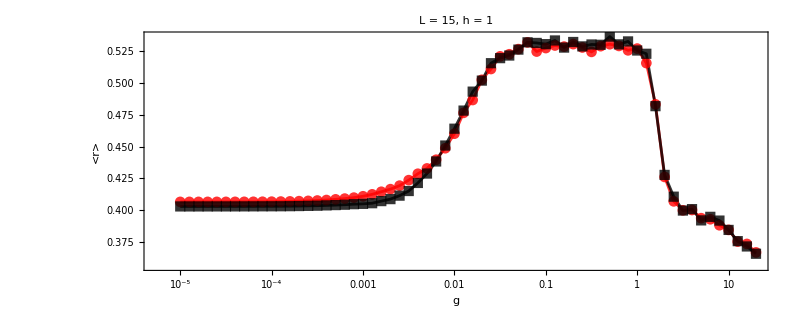

```mathematica
plot15=ListLogLinearPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Directive[Red,Opacity[0.8]],Directive[Black,Opacity[0.8]]},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

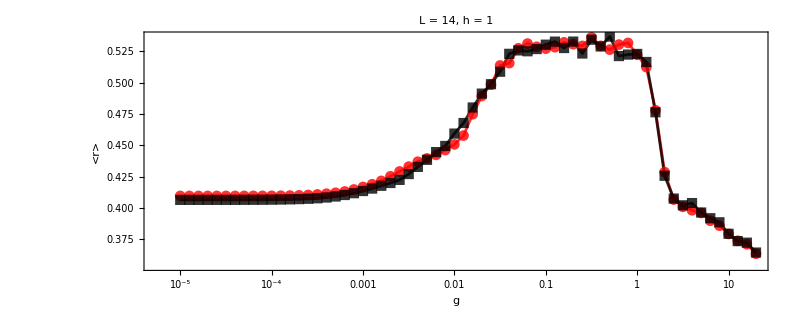

```mathematica
plot14=ListLogLinearPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Directive[Red,Opacity[0.8]],Directive[Black,Opacity[0.8]]},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

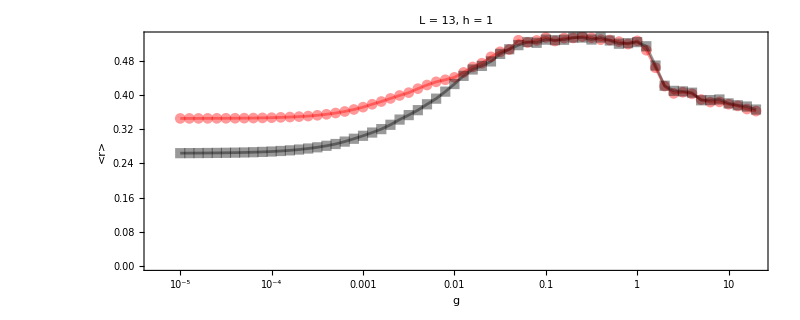

```mathematica
plot13=ListLogLinearPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Directive[Red,Opacity[0.4]],Directive[Black,Opacity[0.4]]},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

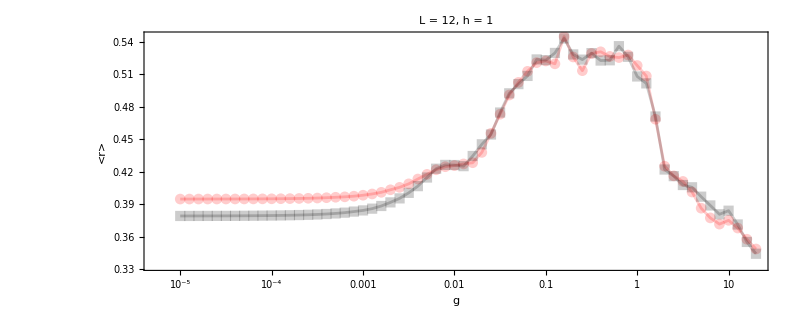

```mathematica
plot12=ListLogLinearPlot[{Transpose[{glist,data[[All,1]][[All,2]]}],Transpose[{glist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Directive[Red,Opacity[0.2]],Directive[Black,Opacity[0.2]]},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

```mathematica
lines=LogLinearPlot[{0.383,0.53},{x,10^-5,10^1.5},PlotStyle->Directive[Brown,Dashed,Thick]];
```

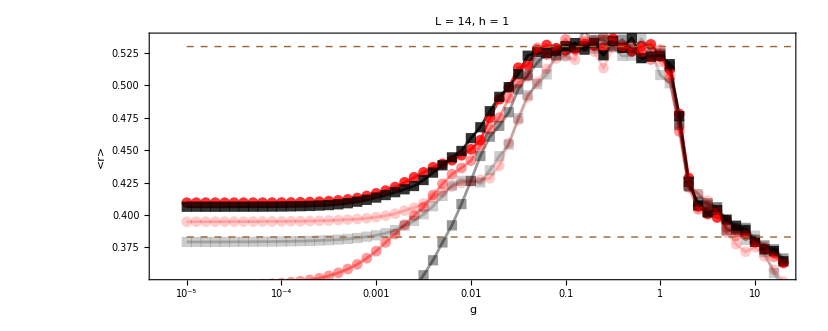

```mathematica
Show[{plot14,plot13,plot12,lines}]
```

```mathematica
data=Import["C:\\Users\\Miguel\\Desktop\\r_L_14_g_1_log_h.m"];
```

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

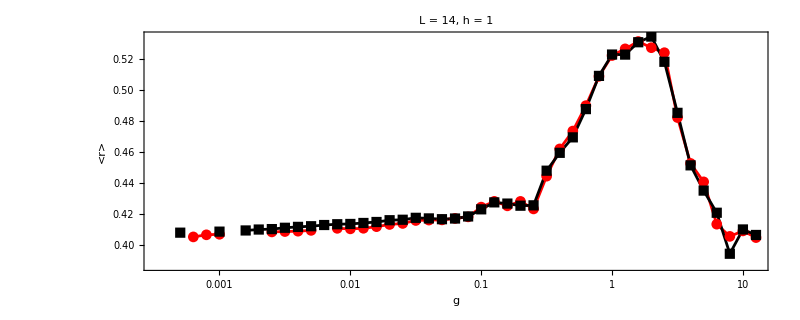

```mathematica
ListLogLinearPlot[{Transpose[{hlist,data[[All,1]][[All,2]]}],Transpose[{hlist,data[[All,2]][[All,2]]}]},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black]]
```

```mathematica
alldata=Import["/Users/pcs/Desktop/Entropy/schmidt modes/r_CLOSED_L_8_g_1_log_h.m"];
```

```mathematica
limits=LogLinearPlot[{0.38,0.53},{x,glist[[1]],glist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListLogLinearPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotTheme->"Detailed",FrameLabel->{Style["h",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20],PlotLegends->Transpose[{{klist,ratios[[All,1]]}}]],limits,PlotRange->All,ImageSize->1000]
```

```mathematica
alldata=Import["/Users/pcs/Desktop/Entropy/schmidt modes/r_CLOSED_L_8_h_1_log_g.m"];
```

```mathematica
limits=LogLinearPlot[{0.38,0.53},{x,hlist[[1]],hlist[[-1]]},PlotStyle->Directive[Gray,Dashed]];
Show[ListLogLinearPlot[Transpose[alldata],Joined->True,PlotMarkers->Automatic,PlotTheme->"Detailed",FrameLabel->{Style["g",20,Black],Style["<r>",Black,20]},FrameStyle->Directive[Black,20],PlotLegends->Transpose[{{klist,ratios[[All,1]]}}],PlotRange->All],limits,PlotRange->All,ImageSize->1000]
```

## Result

```mathematica
L=14;
data=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\r_L_14_h_1_log_g.m"];
```

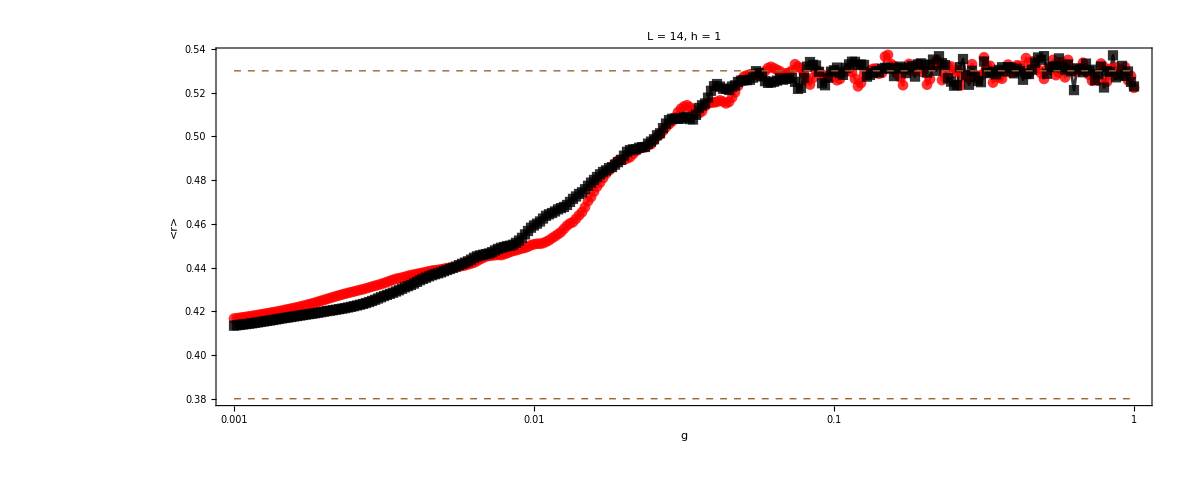

```mathematica
plot=Show[{ListLogLinearPlot[{Sort[data[[All,1]]],Sort[data[[All,2]]]},PlotRange->All,PlotStyle->{Directive[Red,Opacity[0.8]],Directive[Black,Opacity[0.8]]},PlotTheme->"Detailed",FrameLabel->{Style["g",25,Black],Style["<r>",25,Black]},ImageSize->1200,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", h = 1",25,Black],GridLines->None],LogLinearPlot[{0.53,0.38},{x,10^-3,10^0},PlotStyle->Directive[Brown,Dashed,Thick]]},PlotRange->All]
```

```mathematica
Export["L_"<>ToString[L]<>"_ratiosLRN.png",plot,ImageResolution->500]
```

L_14_ratiosLRN.png

```mathematica
L=14;
data2=Import["C:\\Users\\Miguel\\Desktop\\Emmy prethermalization 50 states\\r_L_14_g_1_log_h.m"];
```

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

Min::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

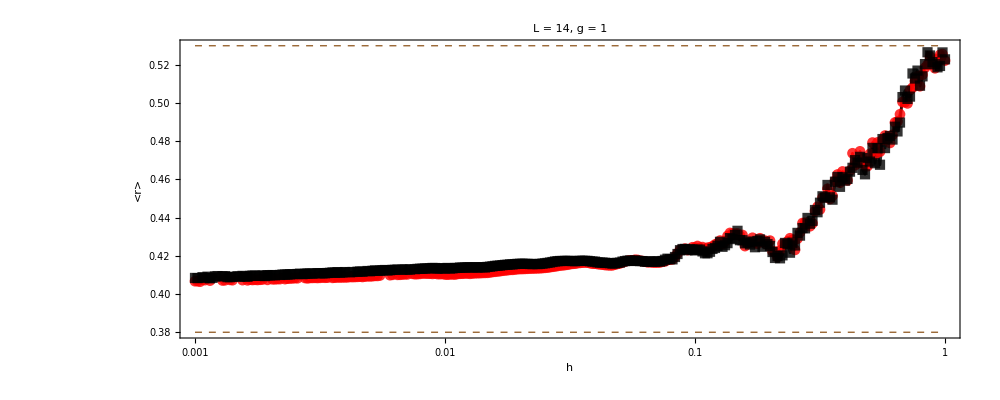

```mathematica
plot2=Show[{ListLogLinearPlot[{Sort[data2[[All,1]]],Sort[data2[[All,2]]]},PlotRange->All,PlotStyle->{Directive[Red,Opacity[0.8]],Directive[Black,Opacity[0.8]]},PlotTheme->"Detailed",FrameLabel->{Style["h",25,Black],Style["<r>",25,Black]},ImageSize->1000,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4,PlotLabel->Style["L = "<>ToString[L]<>", g = 1",25,Black],GridLines->None],LogLinearPlot[{0.53,0.38},{x,10^-3,10^0},PlotStyle->Directive[Brown,Dashed,Thick]]},PlotRange->All]
```

```mathematica
Export["L_"<>ToString[L]<>"_ratiosSRN.png",plot2,ImageResolution->500]
```

L_14_ratiosSRN.png

# Levels

```mathematica
Clear[fun];
fun[g_,vecs_]:=Module[{test=Table[Beven.i,{i,vecs}],overlaps},
overlaps=Table[Abs[Conjugate[i].ini]^2,{i,test}];
First@Ordering[overlaps,-1]
];
```

```mathematica
L=6;
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
glist=Table[10^i,{i,-4,-3,0.0025}];
glist//Length
```

401

```mathematica
Heven//Dimensions
```

{36,36}

```mathematica
newglist=Partition[glist,14];
```

```mathematica
DistributeDefinitions[IsingNNOpenHamiltonian,Beven,fun];
data1={};
data2={};
SetSharedVariable[data1,data2];
Do[
ParallelDo[
	Module[{H, Heven,Hodd,eveneigenval,eveneigenvec,ind},
H = IsingNNOpenHamiltonian[g,1,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[Heven]]]];
AppendTo[data1,Transpose[{ConstantArray[g,36],eveneigenval}]];
ind=fun[g,eveneigenvec];
AppendTo[data2,{g,eveneigenval[[ind]]}];
	]
, {g,k},Method->"CoarsestGrained"];
,{k,newglist}];
(*Export["spectrum_L_"<>ToString[L]<>"_h_1_log_g.m",data1];*)
```

```mathematica
J=1;
h=0.0001;
g=1;
H = IsingNNOpenHamiltonian[h,g,J,L];
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[Heven]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[Hodd]]]];
```

```mathematica
eveneigenvec=ParallelTable[Beven.i,{i,eveneigenvec}];
oddeigenvec=ParallelTable[Bodd.i,{i,oddeigenvec}];
```

```mathematica
allvals=Join[eveneigenval,oddeigenval];
allvecs=Join[eveneigenvec,oddeigenvec];
all=SortBy[Transpose[{allvals,allvecs}],First];
allvals=all[[All,1]];
allvecs=all[[All,2]];
```

```mathematica
ini=coherentstate[qubit[Pi,0],L];
```

```mathematica
norms=ParallelTable[Abs[Conjugate[ini].i]^2,{i,allvecs},DistributedContexts->Full];
```

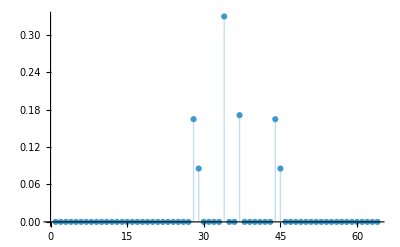

```mathematica
ListPlot[Chop[norms],Filling->Axis,PlotRange->All]
```

```mathematica
compbasis=Table[IdentityMatrix[2^L][[i]],{i,2^L}];
```

1.

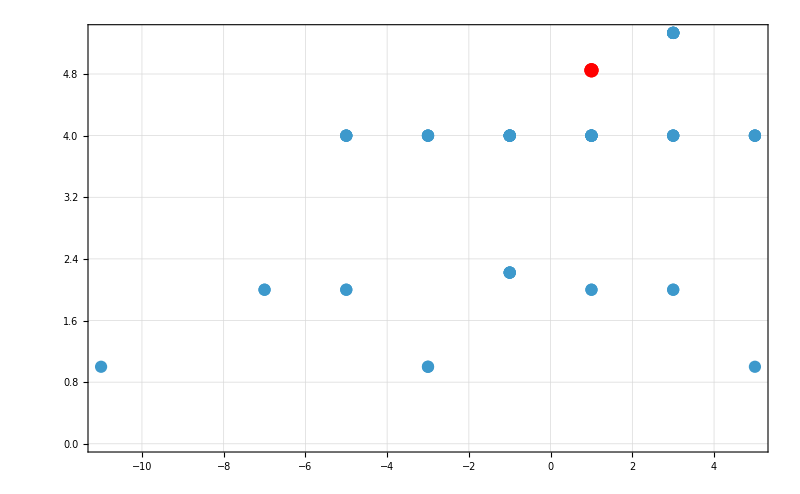

```mathematica
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,compbasis},DistributedContexts->Full];
iprs=ParallelTable[Total[Abs[Conjugate[allvecs].i]^4],{i,compbasis},DistributedContexts->Full];
e1=Chop[Conjugate[ini].H.ini]
ipr1=Total[Abs[Conjugate[allvecs].ini]^4];
iniplot=ListPlot[{{{e1,1/ipr1}}},PlotStyle->Red,PlotRange->All,PlotTheme->"Detailed",ImageSize->800];
Show[{ListPlot[Transpose[{energies,1/iprs}],PlotRange->All,PlotTheme->"Detailed",ImageSize->800],iniplot}]
```

## levels

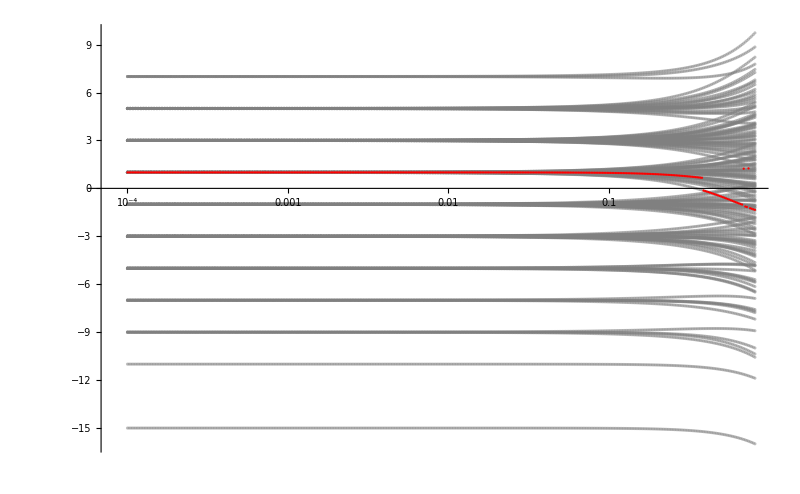

```mathematica
uno=ListLogLinearPlot[data2,PlotRange->All,PlotStyle->Directive[Red,PointSize[0.002]],ImageSize->800];dos=ListLogLinearPlot[data1,PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->800];
Show[{dos,uno}]
```

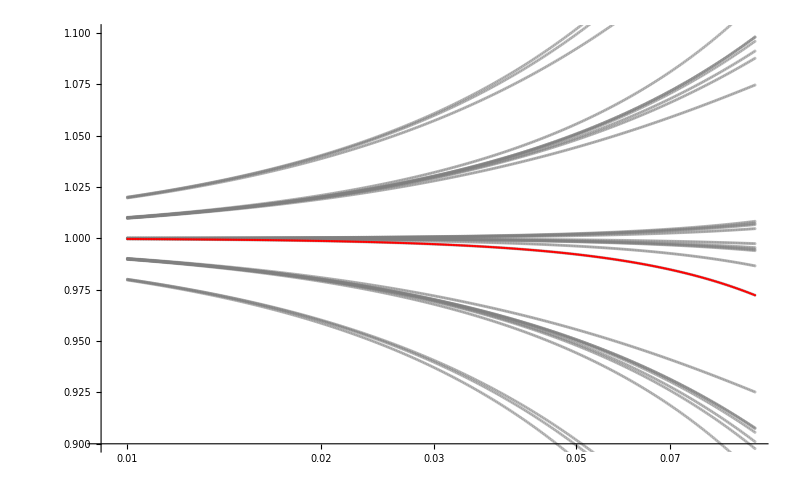

```mathematica
uno=ListLogLinearPlot[data2,PlotRange->{All,{0.9,1.1}},PlotStyle->Directive[Red,PointSize[0.002]],ImageSize->800];dos=ListLogLinearPlot[data1,PlotRange->{All,{0.9,1.1}},PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->800];
Show[{dos,uno}]
```

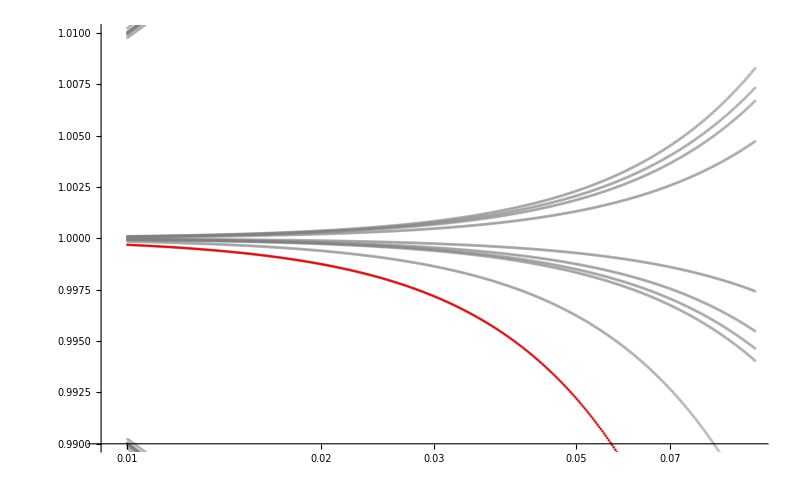

```mathematica
uno=ListLogLinearPlot[data2,PlotRange->{All,{0.99,1.01}},PlotStyle->Directive[Red,PointSize[0.002]],ImageSize->800];dos=ListLogLinearPlot[data1,PlotRange->{All,{0.99,1.01}},PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->800];
Show[{dos,uno}]
```

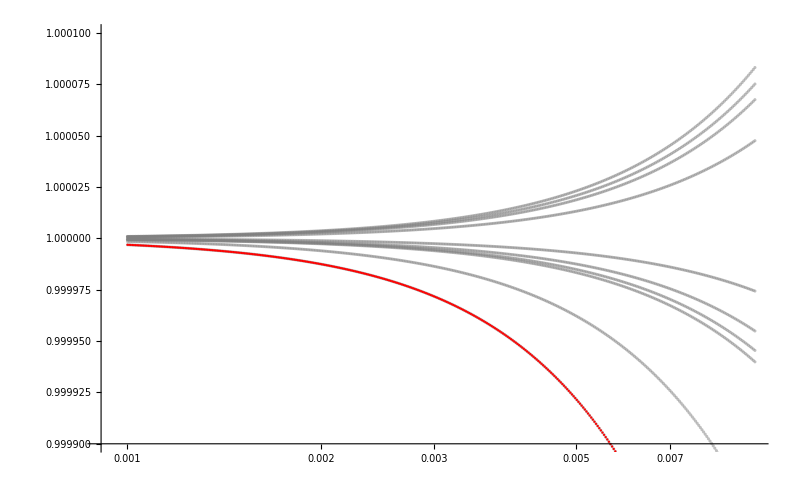

```mathematica
uno=ListLogLinearPlot[data2,PlotRange->{All,{0.9999,1.0001}},PlotStyle->Directive[Red,PointSize[0.002]],ImageSize->800];dos=ListLogLinearPlot[data1,PlotRange->{All,{0.9999,1.0001}},PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->800];
Show[{dos,uno}]
```

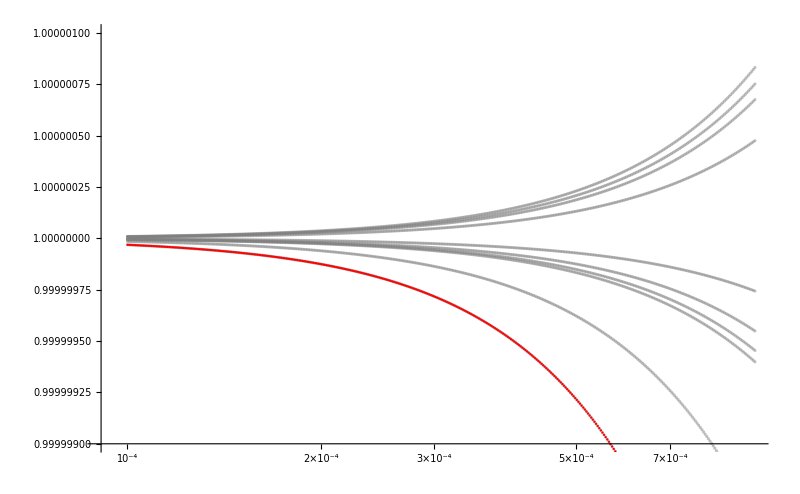

```mathematica
uno=ListLogLinearPlot[data2,PlotRange->{All,{0.999999,1.000001}},PlotStyle->Directive[Red,PointSize[0.002]],ImageSize->800];dos=ListLogLinearPlot[data1,PlotRange->{All,{0.999999,1.000001}},PlotStyle->Directive[Gray,Opacity[0.5]],ImageSize->800];
Show[{dos,uno}]
```

# Code comparison

```mathematica
Get["C:\\Users\\Miguel\\Downloads\\QMB.wl"]
```

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
{hx,hz,J,L}={-1,-1/2,-1,12};
```

```mathematica
Ha=-IsingHamiltonian[hx, hz, J, L,BoundaryConditions->"Periodic"];
```

```mathematica
system=BlockDiagonalize[Ha, Symmetry->"Translation"];
```

```mathematica
{eigenvalb,eigenvecb}=Transpose[Sort[Transpose[Eigensystem[system]]]];
```

Eigensystem::arh: Because finding 352 out of the 352 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Eigensystem::arh: Because finding 335 out of the 335 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

Eigensystem::arh: Because finding 344 out of the 344 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

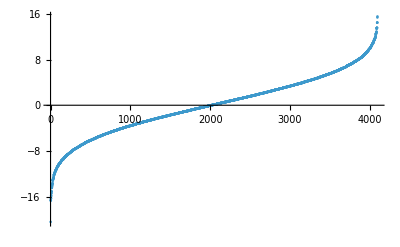

```mathematica
eigenvalb//ListPlot
```

## OLD CODE

```mathematica
Clear[IsingNNClosedHamiltonian];
IsingNNClosedHamiltonian[h_,g_,J_,L_] := Module[{NNIndices},
	NNIndices=Normal[SparseArray[Thread[{#,Mod[#+1,L,1]}->3],{L}]&/@Range[L]];
	-Normal[Total[{h*Pauli[#]+g*Pauli[3#]&/@IdentityMatrix[L],J*(Pauli/@NNIndices)},2]]
]
```

```mathematica
L=3;
```

```mathematica
dim=2^L; (*Dimension of the Hilbert space*)
basisStates=IntegerDigits[Range[0,dim-1],2,L];
TranslateState[state_List]:=RotateLeft[state];
orbits={};
visited=Association[];
Do[If[!KeyExistsQ[visited,state],orbit=NestList[TranslateState,state,L-1];
orbit=DeleteDuplicates[orbit];
(*Mark all states in the orbit as visited*)Scan[(visited[#]=True)&,orbit];
AppendTo[orbits,orbit];],{state,basisStates}];
(*Creating momentum states*)
momentumEigenstates={};
Do[orbitSize=Length[orbit];
Do[k=2 Pi m/orbitSize;
stateSum=ConstantArray[0,dim];
Do[translatedState=Nest[TranslateState,orbit[[1]],n];
index=Position[basisStates,translatedState][[1,1]];
stateSum[[index]]+=Exp[-I k n];,{n,0,orbitSize-1}];
normalizedState=stateSum/Norm[stateSum];
AppendTo[momentumEigenstates,{k,normalizedState}];,{m,0,orbitSize-1}];,{orbit,orbits}];
(*Sorting everything*)
ks=First/@momentumEigenstates;
perm=OrderingBy[momentumEigenstates,First];
sortedKEigen=ks[[perm]];
sortedStates=(Last/@momentumEigenstates)[[perm]];
sortedPairs=Transpose[{sortedKEigen,sortedStates}];
dimensions=Tally[sortedKEigen];
```

```mathematica
Hb=IsingNNClosedHamiltonian[1,1/2,1,3];
U=Transpose[sortedStates];
HMomentumBasis=ConjugateTranspose[U].Hb.U;
posByK=GroupBy[Range@Length[sortedKEigen],sortedKEigen[[#]]&];
blocks={};
Do[
AppendTo[blocks,HMomentumBasis[[i[[1]];;i[[-1]],i[[1]];;i[[-1]]]]];
,{i,posByK}];
eigen=ParallelTable[Eigensystem[i],{i,blocks},DistributedContexts->Full];
transforms=Table[Transpose[Chop[sortedStates[[i]]]],{i,posByK}];
eigenvecs={};
Do[
a=ParallelTable[Chop[transforms[[j]].i],{i,eigen[[j,2]]},DistributedContexts->Full];
AppendTo[eigenvecs,a];
,{j,Length[transforms]}];
allvecs=Flatten[eigenvecs,1];
allvals=Flatten[Chop[eigen[[All,1]]]];
alldata=Transpose[{Chop[eigen[[All,1]]],eigenvecs}];
```

```mathematica
test=ParallelTable[Abs[N[Conjugate[i].j]]^2,{i,allvecs},{j,allvecs}];
```

```mathematica
MatrixForm[Chop[test]]
```

(1.30489 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4482.54 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 934.927 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 168.896 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 13.0902 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.90983 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 13.0902 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.90983)

```mathematica
Table[Total[Abs[i]^2],{i,allvecs}]//N//Chop
```

{1.14232,66.9518,30.5766,12.996,3.61803,1.38197,3.61803,1.38197}